```mathematica
(*Part 1A*)
```

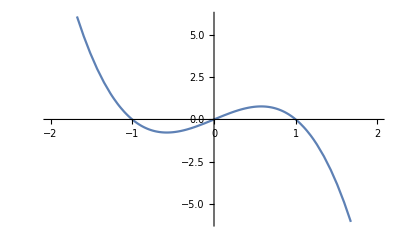

```mathematica
Plot[2y-2y^3,{y,-2,2}]
```

```mathematica
(*Steady States at y=-1, y=0, y=1
y=-1 is stable
y=0 is unstable
y=1 is stable*)

(*Evident from graph as well as fact that f'(y)=2-6y^2 so that
f'(1)=f'(-1)=-4 < 0 so those are stable
and f'(0)=2 > 0 so that one is unstable*)
```

```mathematica
Integrate[1/(1-y^2),y]
```

-1/2 Log[1-y]+1/2 Log[1+y]

```mathematica
Integrate[1/(2y-2y^3),y]
```

Log[y]/2-1/4 Log[1-y^2]

```mathematica
(*Initial Value 1 is y(0) = 1.5
Initial Value 2 is y(0) = 0.5*)
```

```mathematica
vv1 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==1.5},y,{t,0,20}]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
vv2 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==.5},y,{t,0,20}]
```

InterpolatingFunction[{{0., 20.}}, <>]

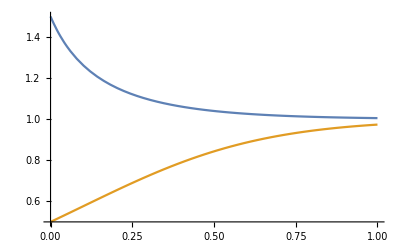

```mathematica
Plot[{vv1[t],vv2[t]},{t,0,1}]
```

```mathematica
(*Problem 1B*)
(*Steady state if e^(-y)=0 or sin(y)=0
First condition will never happen
sin(y)=0 if y=n*Pi for any integer n*)
(*It holds that f'(y)=e^(-y)(cos(y)-sin(y)) *)
(*Here is verification*)
D[Exp[-y]*Sin[y],y]
```

ⅇ^-y Cos[y]-ⅇ^-y Sin[y]

```mathematica
(*Steady states occur at n*Pi
e^(-y)>0 everywhere so we care about the sign of the other term
If y=2*n*Pi for integer n then cos(y)=1 so f'(y)>0 making those steady states unstable
If y=(2*n+1)*Pi for integer n then cos(y)=-1 so f'(y)<0 making those steady states stable *)
```

```mathematica
(*Here are two sample solutions*)
```

```mathematica
ww1 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==1},y,{t,0,20}];
```

```mathematica
ww2 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==2},y,{t,0,20}];
```

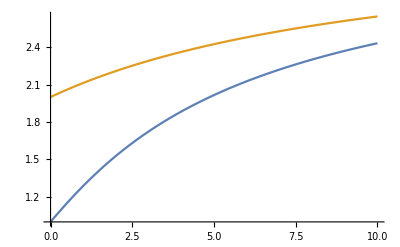

```mathematica
Plot[{ww1[t],ww2[t]},{t,0,10}]
```

```mathematica
(*Problem 2*)
(*Need a function with zeros at 0,1,2,3. For simplicity I will try a polynomial*)
(*It will need to have the form f(y)=Ky(y-1)(y-2)(y-3) *)
(*I will compute f'(y) to get info about steady states*)
Expand[D[y(y-1)(y-2)(y-3),y]]
```

-6+22 y-18 y^2+4 y^3

```mathematica
fPrime[y_]:=-6+22 y-18 y^2+4 y^3
```

```mathematica
{fPrime[0],fPrime[1],fPrime[2],fPrime[3]}
```

{-6,2,-2,6}

```mathematica
(*This shows that our properties are satisifed*)
(*More generally, it will hold for all K>0 so there is more than one system that is valid*)
```

```mathematica
(*Problem 3*)
```

```mathematica
Manipulate[Plot[{r*Log[y],y-1},{y,-10,10}],{r,-2,5}]
```

```mathematica
(*If y=1, the ln(y)=0 so the value of r is irrelevant*)
```

```mathematica
(*Part B*)
(*Equation is now u'=-r ln(u+1) + u*)
(*Part C*)
(* If we assume that ln(u+1) = u - (1/2)u^2 then when expanding the part b equation using that assumption we have
u' = -r (u - (1/2)u^2 ) + u
u' = -r*u + (1/2)r*u^2 + u  (1)
When you expand the part c equation you end up with
u' = (r/2)u( -2 + 2/r + u)
u' = u( -r + 1 + r*u/2)
u' = -r*u + u + r*u^2/2   (2)
Equation (1) matches equation (2) above so the given equation for u' is valid*)
```

```mathematica
Manipulate[Plot[{(r/2)*u((-r+1)(2/r)+u),u(mu+u)},{u,-0.2,0.2}],{r,0.8,1.2},{mu,-0.2,0.2}]
```

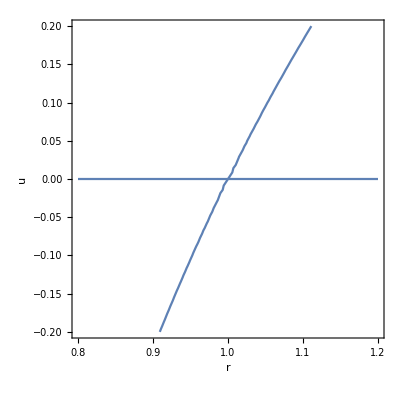

```mathematica
ContourPlot[(r/2)*u((-r+1)(2/r)+u)==0,{r,0.8,1.2},{u,-0.2,0.2}, AxesLabel->Automatic]
```

```mathematica
(*The system is the same except for a constant factor in front and mu equal to a function of r *)
(*TODO: WRITE MORE LATER*)
```

```mathematica
(*Problem 4*)
Manipulate[Plot[1+r*y+y^2,{y,-3,3}],{r,-3,3}]
```

```mathematica
(*For large positive and negative values, y' will be positive. 
The quadratic equation 1+r*y+y^2 has a discriminant of r^2-4
Meaning that if |r|<2 there are no real roots so the equation is positive everywhere. 
If r=2 or r=-2 then there is one unstable steady state at y=-1 and y=1 respectively
If |r|>2 there are two steady states at (-r-sqrt(r^2-4))/2 and(-r+sqrt(r^2-4))/2
			The first one is stable and the second one is unstable respectively
This is an example of Saddle Node Bifurcation*)
```

```mathematica
yPrimeFunc[r_]:=1+r*y+y^2;
```

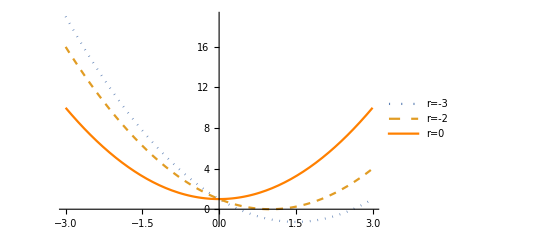

```mathematica
(*This shows the phase diagram for 
r=-3 (two steady states), 
r=-2 (one steady state), and 
r=2 (no steady states)*)
Plot[{yPrimeFunc[-3],yPrimeFunc[-2],yPrimeFunc[0]},{y,-3,3},PlotLegends->{"r=-3","r=-2","r=0"},PlotStyle->{Dotted,Dashed,Orange}]
```

```mathematica
(*It holds that f'(y)=r+2y
For a given r value, the two steady state y values are described by
y1(r) = (-r+sqrt(r^2-4))/2
y2(r) = (-r-sqrt(r^2-4))/2

For y1 it holds that r+2y = sqrt(r^2-4) ≥ 0 so that branch is unstable
For y2 it holds that r+2y = -sqrt(r^2-4) ≤ 0 so that branch is stable 

The bifurcation points occur when r+2y=0 thus (r,y) is equal to (-2,1) and (2,-1)

The plot below shows the stable and unstable branches as well as the bifurcation points as black dots*)
```

```mathematica
prob4Plot = Plot[{(-r+Sqrt[r^2-4])/2,(-r-Sqrt[r^2-4])/2},{r,-6,6}, PlotStyle->{Dashed,Thick},AxesLabel->Automatic, PlotLegends->{"Unstable","Stable"}];
```

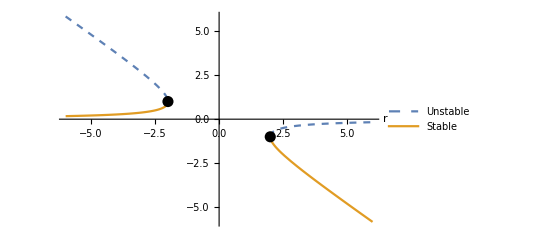

```mathematica
Show[prob4Plot,Graphics[{PointSize[0.02],Point[{-2,1}]}],Graphics[{PointSize[0.02],Point[{2,-1}]}]]
```

```mathematica
ff[r_]:=y*(r-Exp[y])
```

```mathematica
(*Problem 5*)
Manipulate[Plot[ff[r],{y,-10,2}],{r,-10,10}]
```

```mathematica
(*For large positive values of y it holds that r won't matter as -y*e^(y) will be a large negative number
For large negative values of y it holds that e^(y) is near zero thus the graph will be similar to r*y
So it r<0 and y negative then y' will be positive, but if r>0 and y negative then y' will be negative *)
```

```mathematica
(*The steady states will occur when y=0 or r=e^y
If r≤0 then there will only be one steady state at y=0 an dit will be stable
If r>0 then there will be two steady states at y=0 and y=ln(r). The lower one is unstable and the higher value is stable. *)
```

```mathematica
ff[r_]:=y*(r-Exp[y])
```

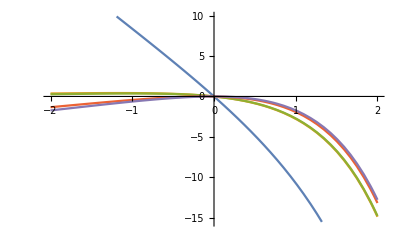

```mathematica
(*r=-5,0,5 Plot*)Plot[{ff[-8],ff[-0.05],ff[0],ff[0.8],ff[1]},{y,-2,2}]
```

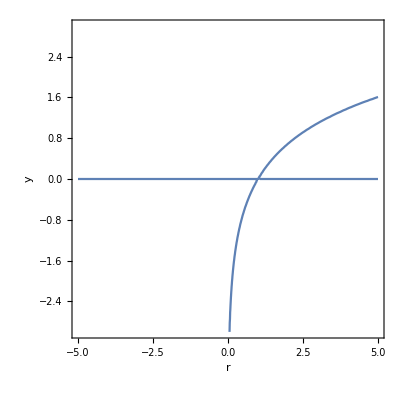

```mathematica
ContourPlot[y*(r-Exp[y])==0,{r,-5,5},{y,-3,3},AxesLabel->Automatic]
```

```mathematica
D[y*(r-Exp[y]),y]
```

-ⅇ^y+r-ⅇ^y y

```mathematica
(*TODO: PLOT WHICH PARTS OF ABOVE GRAPH ARE UNSTABLE/STABLE*)
```

```mathematica
(*Problem 6*)
Manipulate[Plot[y+r*y/(1+y^2),{y,-1,1}],{r,-5,15}]
```

```mathematica
ff[r_]:=y+r*y/(1+y^2)
```

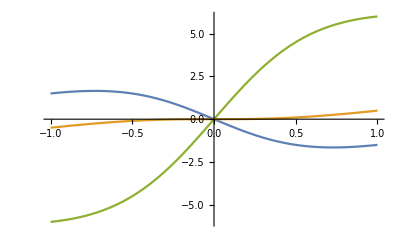

```mathematica
(*r=-5,0,5 Plot*)Plot[{ff[-5],ff[-1],ff[10]},{y,-1,1}]
```

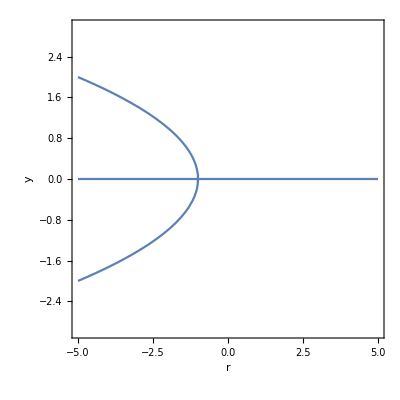

```mathematica
ContourPlot[y+r*y/(1+y^2)==0,{r,-5,5},{y,-3,3},AxesLabel->Automatic]
```

```mathematica
D[y+r*y/(1+y^2),y]
```

1-(2 r y^2)/((1+y^2)^2)+r/(1+y^2)